```mathematica
NA = 6.0221367 10^23;
Dtot=10^-11;
kf=10^6  / NA;
kd=10^3;
sigma=5 10^-8;
kD=4*Pi*sigma*Dtot;
h=(1+kf/kD)*Sqrt[Dtot]/sigma;
a=kd*Sqrt[Dtot]/sigma;
r0=sigma;
t=0.01;
```

```mathematica
ciccio=N[Solve[{x+y+z==h, x*y+y*z+x*z==kd,x*y*z==a},{x,y,z}]];
alpha=ciccio[[1,1,2]];
beta = ciccio[[1,2,2]];
gamma=ciccio[[1,3,2]];
```

```mathematica
W[x_,y_]:=Exp[2*x*y+y^2]*Erfc[x+y];
frac[x_,y_,z_]:=(x*(z+x)*(x+y))/((z-x)*(x-y));
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[Dtot]);
term1[r_]:=1/Sqrt[4*Pi*t]*(Exp[-(r-r0)^2/(4*Dtot*t)]+Exp[-(r+r0-2*sigma)^2/(4*Dtot*t)]);
term2[r_]:=frac[alpha,beta,gamma]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),alpha*Sqrt[t]];
term3[r_]:=frac[beta,gamma,alpha]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),beta*Sqrt[t]];
term4[r_]:=frac[gamma,alpha,beta]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),gamma*Sqrt[t]];
```

```mathematica
f[r_]:=4*Pi*r^2*Re[coeff[r]*(term1[r]+term2[r]+term3[r]+term4[r])]
```

c = N[Integrate[f[r], {r, 1, Infinity}]]

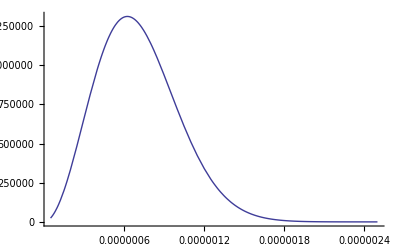

```mathematica
Plot[f[r], {r,sigma,sigma 50}]
```

```mathematica
out=Table[{r,f[r]},{r,sigma,sigma 50,(sigma 50 - sigma) / 50}] // N
```

{{5.×10^-8,24194.9},{9.9×10^-8,90439.2},{1.48×10^-7,193722.},{1.97×10^-7,326458.},{2.46×10^-7,479211.},{2.95×10^-7,641526.},{3.44×10^-7,802788.},{3.93×10^-7,953052.},{4.42×10^-7,1.08374×10^6},{4.91×10^-7,1.18818×10^6},{5.4×10^-7,1.2619×10^6},{5.89×10^-7,1.30277×10^6},{6.38×10^-7,1.31087×10^6},{6.87×10^-7,1.28824×10^6},{7.36×10^-7,1.23848×10^6},{7.85×10^-7,1.16631×10^6},{8.34×10^-7,1.07705×10^6},{8.83×10^-7,976213.},{9.32×10^-7,869096.},{9.81×10^-7,760465.},{1.03×10^-6,654356.},{1.079×10^-6,553953.},{1.128×10^-6,461563.},{1.177×10^-6,378650.},{1.226×10^-6,305935.},{1.275×10^-6,243511.},{1.324×10^-6,190990.},{1.373×10^-6,147637.},{1.422×10^-6,112501.},{1.471×10^-6,84520.6},{1.52×10^-6,62615.8},{1.569×10^-6,45748.5},{1.618×10^-6,32968.2},{1.667×10^-6,23436.2},{1.716×10^-6,16436.},{1.765×10^-6,11372.7},{1.814×10^-6,7764.69},{1.863×10^-6,5231.32},{1.912×10^-6,3478.21},{1.961×10^-6,2282.38},{2.01×10^-6,1478.19},{2.059×10^-6,944.949},{2.108×10^-6,596.273},{2.157×10^-6,371.416},{2.206×10^-6,228.388},{2.255×10^-6,138.644},{2.304×10^-6,83.0927},{2.353×10^-6,49.1667},{2.402×10^-6,28.7238},{2.451×10^-6,16.5687},{2.5×10^-6,9.43675}}

```mathematica
Export["p_rev.tsv",out]
```

p_rev.tsv